```mathematica
R=0.3;
U[r_]:=10Piecewise[{{1/2 NIntegrate[(1-Exp[-10(2 √(R^2-r^2(1-μ^2)))])Exp[-(r μ-√(R^2-r^2(1-μ^2)))],{μ,√(1-(R/r)^2),1}],r≥R},{NIntegrate[1-Cosh[10 r μ]Exp[-10 √(R^2-r^2(1-μ^2))],{μ,0,1}],r<R}}]
EWm=Table[i,{i,0,1,0.01}];
Sol=Table[{EWm[[i]],U[EWm[[i]]]},{i,1,Length[EWm]}];
(*EPlus=Import["/home/artem/projects/solver/build/Solve/energy1d_R_0.txt","table"];*)
EPlus=Import["/home/artem/projects/data_claster/sphere1500k/energy1d_R_0.txt","table"];
```

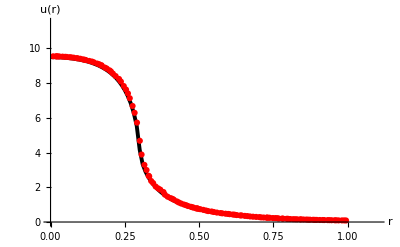

```mathematica
Show[ListLinePlot[Sol,PlotRange->{{0,1.1},{0.01,11.5}},PlotStyle->Directive[Black,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],AxesLabel->{"StyleBox[\"r\",FontSlant->\"Italic\"]","uStyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"r\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]"}],
ListPlot[EPlus,PlotStyle->Directive[PointSize[0.011],Red]]]
```

```mathematica
i=ii[s]/.DSolve[{D[ii[s],s]+(a+b)ii[s]==b S+a Q, ii[0]==ii0},ii[s],s][[1]]//FullSimplify
```

(ⅇ^(-((a+b) s)) (a ii0+b ii0-a Q-b S+ⅇ^((a+b) s) (a Q+b S)))/(a+b)

```mathematica
i/.(a+b)->k//Expand
```

(a ⅇ^(-k s) ii0)/k+(b ⅇ^(-k s) ii0)/k+(a Q)/k-(a ⅇ^(-k s) Q)/k+(b S)/k-(b ⅇ^(-k s) S)/k

```mathematica
(i/.(a+b)->k)/.{Exp[k s]->(1+k s), Exp[-k s]->(1-k s)}//Simplify
```

-((-1+k s) (a (ii0+k Q s)+b (ii0+k s S)))/k

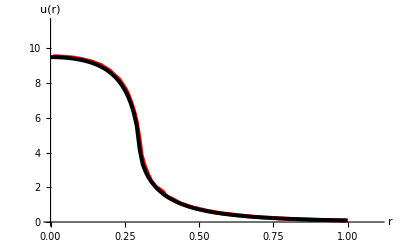

```mathematica
EPlus=Sort[EPlus,#1[[1]]<#2[[1]]&];
Show[ListLinePlot[EPlus,PlotRange->{{0,1.1},{0.01,11.5}},PlotStyle->Directive[Red,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],AxesLabel->{"StyleBox[\"r\",FontSlant->\"Italic\"]","uStyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"r\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]"}],
ListLinePlot[Sol,PlotStyle->Directive[Thickness[0.007],Black]]]
```

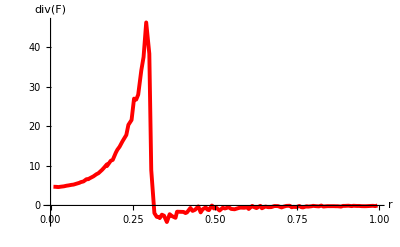

```mathematica
ListLinePlot[EPlus,PlotRange->All,PlotStyle->Directive[Red,Thickness[0.007]],AxesStyle->Directive[Black, 17(*,Arrowheads[.04]*)],AxesLabel->{"r","div(F)"}]
```